```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

FeynCalcExternal::shdw: Symbol FeynCalcExternal appears in multiple contexts {FeynCalc`,Global`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_],LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->NotebookDirectory[]]
```

Successfully patched FeynArts.

```mathematica
diags=InsertFields[CreateTopologies[0,0->3],{}->{V[1,{a1}],V[1,{a2}],V[1,{a3}]},InsertionLevel->{Particles},Model->FileNameJoin[{NotebookDirectory[],"QCD"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"QCD"}]];
```

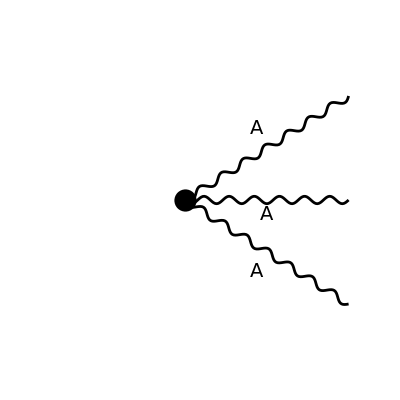

```mathematica
Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{},OutgoingMomenta->{p1,p2,p3},LoopMomenta->{},ChangeDimension->4,List->False]
```

Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] (-g Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]+g Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p3]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p2]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]])

```mathematica
FCClearScalarProducts[];
(*SetMandelstam[x,{ p1 , p2, p3} ,{ 0 , 0 , 0} ];*)
```

```mathematica
amp[1]=amp[0] // Contract //SUNSimplify
```

-g (Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]

```mathematica
amp[2] = amp[1] // ExpandScalarProduct
```

-g (Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]

```mathematica
amp[3] =FeynAmpDenominatorExplicit[amp[2]]
```

-g (Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]

```mathematica
amp[4] = amp[3]// ExpandScalarProduct  // Simplify
```

-g (Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]

```mathematica
amp[5]=FeynCalcExternal[amp[4]]
```

-g (SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]) SUNF[a1,a2,a3]

```mathematica
amp[6] = amp[5]/.SUNF[___]->1
```

-g (SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])

```mathematica
amp[7]=amp[6]/. SP[x_,y_]->mp[x,y]
```

-g (mp[p1,Polarization[p3,-ⅈ]] mp[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-mp[p2,Polarization[p3,-ⅈ]] mp[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-mp[p1,Polarization[p2,-ⅈ]] mp[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+mp[p3,Polarization[p2,-ⅈ]] mp[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+mp[p2,Polarization[p1,-ⅈ]] mp[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-mp[p3,Polarization[p1,-ⅈ]] mp[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])

```mathematica
tree3point = amp[7]/.Polarization[x_,-I]->pol[x]
```

-g (mp[p1,pol[p3]] mp[pol[p1],pol[p2]]-mp[p2,pol[p3]] mp[pol[p1],pol[p2]]-mp[p1,pol[p2]] mp[pol[p1],pol[p3]]+mp[p3,pol[p2]] mp[pol[p1],pol[p3]]+mp[p2,pol[p1]] mp[pol[p2],pol[p3]]-mp[p3,pol[p1]] mp[pol[p2],pol[p3]])

```mathematica
Tree3Point[p1_,p2_,p3_,pol_]:=-g (mp[p1,pol[p3]] mp[pol[p1],pol[p2]]-mp[p2,pol[p3]] mp[pol[p1],pol[p2]]-mp[p1,pol[p2]] mp[pol[p1],pol[p3]]+mp[p3,pol[p2]] mp[pol[p1],pol[p3]]+mp[p2,pol[p1]] mp[pol[p2],pol[p3]]-mp[p3,pol[p1]] mp[pol[p2],pol[p3]])
```

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"TreePointFunctions.wl"}],{Tree3Point}]
```

```mathematica
diags2=InsertFields[CreateTopologies[0,0->4],{}->{V[1,{a1}],V[1,{a2}],V[1,{a3}],V[1,{a4}]},InsertionLevel->{Particles},Model->FileNameJoin[{NotebookDirectory[],"QCD"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"QCD"}]];
```

```mathematica
amp2[0]=FCFAConvert[CreateFeynAmp[diags2, PreFactor->1],IncomingMomenta->{},OutgoingMomenta->{p1,p2,p3,p4},LoopMomenta->{},ChangeDimension->4,List->False]
```

```mathematica
amp2[1]=amp2[0] // Contract //SUNSimplify//FeynAmpDenominatorExplicit// ExpandScalarProduct  // Simplify//FeynCalcExternal
```

```mathematica
amp2[1] /. SP[x_,x_]->0/.SP[y_,Polarization[y_,-I]]->0
```

```mathematica
FeynCalcExternal[%]
```

```mathematica
%//SUNSimplify
```

```mathematica
SUNTrace[%]
```